# Наилучшее среднеквадратичное приближение (Лагерр)

Выполнил:Сайков Константин
																																	Группа:ПМ1801

```mathematica
Lagerra[n_,alfa_]:=ⅇ^x*D[ⅇ^-x*x^(n+alfa),{x,n}]/n!//FullSimplify
a[fun_,n_,alfa_]:=Integrate[fun*ⅇ^-x*x^alfa*Lagerra[n,alfa],{x,0,Infinity}];
approx[fun_,n_,alfa_]:=Total[Table[N@Lagerra[k,alfa]*a[fun,k,alfa]//N,{k,0,n}]]//FullSimplify
```

```mathematica
polynomial=approx[x^5,5,0];
```

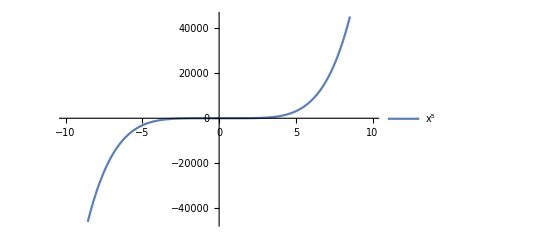

```mathematica
Plot[x^5,{x,-10,10},PlotLegends->{"x^5"}]
```

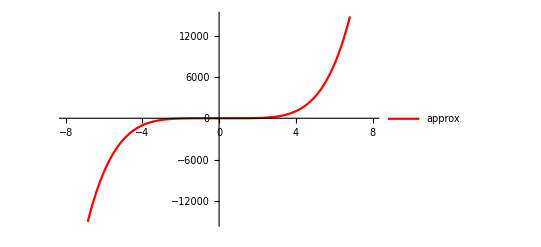

```mathematica
Plot[polynomial/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"approx"}]
```

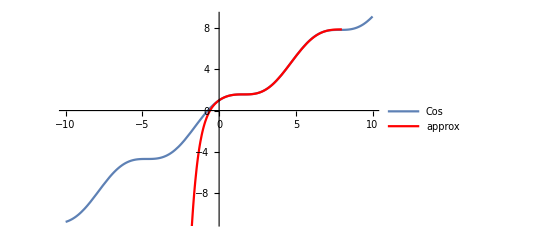

```mathematica
polynomial1=approx[Cos[x]+x,15,0];
Show[{Plot[Cos[x]+x,{x,-10,10},PlotLegends->{"Cos"}],Plot[polynomial1/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"approx"}]}]
```

A если повысить степень?

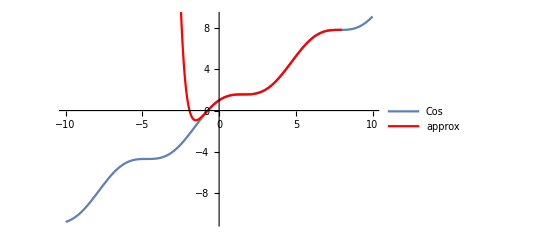

```mathematica
polynomial1=approx[Cos[x]+x,25,0];
Show[{Plot[Cos[x]+x,{x,-10,10},PlotLegends->{"Cos"}],Plot[polynomial1/.x->k,{k,-8,8},PlotStyle->Red,PlotLegends->{"approx"}]}]
```

Теперь чуть больше похоже на то, что было